## Pi3 Number Visibility

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
series=(100#1+10#2+#3)&@@@Partition[RealDigits[Pi,10,30002][[1,2;;]],3];
```

## SDL Complexity

```mathematica
<<sdl.mx
```

```mathematica
result=sdl[series]
```

{0.1007,0.974157}

## Visibility

```mathematica
<<visibility.mx
```

```mathematica
links=naturalVisibilityLinks[series];
```

```mathematica
natGraph=Graph[links, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[natGraph]//Mean//N]
```

```mathematica
count=VertexDegree[natGraph]//Counts
```

<|8→349,3→2004,7→534,6→708,9→290,15→74,2→2303,5→1052,4→1508,18→43,17→50,12→175,14→92,11→205,21→33,23→18,27→7,10→217,13→102,19→40,32→2,16→52,28→5,25→16,22→27,26→14,31→8,30→7,29→5,39→3,41→1,24→8,20→33,33→3,43→1,34→3,46→1,53→1,38→2,35→1,37→2|>

```mathematica
If[count[1]<3,count[1]=.];
```

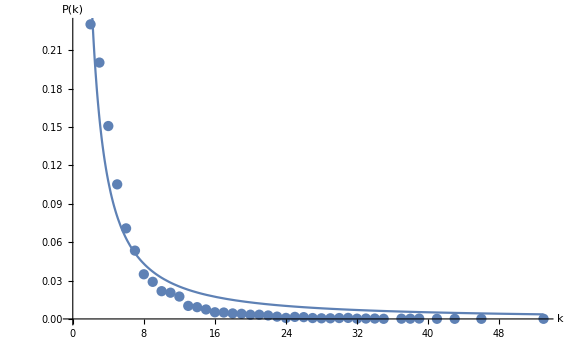
{{C→0.665877,γ→1.31572},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```

## Horizontal Visibility

```mathematica
horlinks=horizontalVisibilityLinks[series];
```

```mathematica
hg=Graph[horlinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[hg]//Mean//N]
```

```mathematica
count=VertexDegree[hg]//Counts
```

<|5→895,3→2200,6→621,8→288,2→3622,4→1327,7→421,12→56,18→5,9→180,10→149,15→17,11→110,16→16,21→2,14→32,13→44,17→7,19→4,20→3|>

```mathematica
If[count[1]<3,count[1]=.];
```

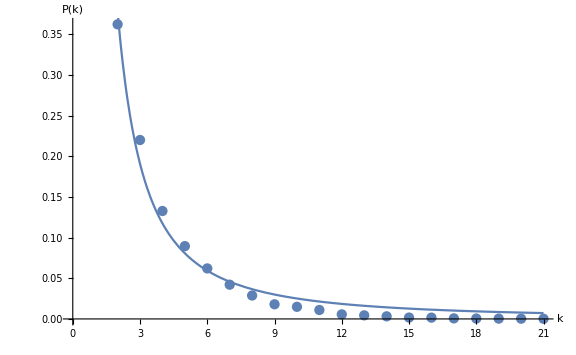
{{C→1.21288,γ→1.68399},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```